# Notebook for Maintaining Multiple Needs (2022)

Connor McShaffrey & Randall Beer

## Importing Dynamica

Dynamica is a free package for doing analysis on smooth dynamical systems in Mathematica, designed and maintained by Randall Beer. A tutorial for the package, as well as the package itself, can be found on his personal website: https://rdbeer.pages.iu.edu/

```mathematica
Needs["Dynamica`"];
```

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

## Dynamical Systems Analyses from the Paper

This section replicates the figures from Maintaining Multiple Needs (2022), as well as related figures that did not make their way into the paper due to a lack of space, but may still be useful to the reader. For any questions regarding how the figures fit together, or why certain decisions were made in the workflow, please refer to the paper. Some of the figures were generated in Python, and those will be included on GitHub in a separate code file. Note that the paper bounces back-and-forth between the work done in Mathematica vs Python.

### Protocell Specifications

These are the three dynamical systems that I use in the paper. The first one is the protocell with multiple metabolites that does not chemotax, the second one is the protocell with reduced dimensionality that only has one metabolite, and the third one is the original protocell with multiple metabolites but with the introduction of chemotaxis. In all of the cases where there is shading, I am showing the viability limits imposed on the protocell, which are specified in the paper.

```mathematica
PC=DynamicalSystem[
{γ*B^h/(B^h+K1^h)*N1-kd*A,
γ*A^h/(A^h+K1^h)*F-kd*B},
{{A,-0.2,20},{B,-0.2,20}},
{{kd,0,1},{γ,0,1},{K1,0,5},{h,0,4},{N1,0,50},{F,0,50}}];
```

```mathematica
PR=DynamicalSystem[
{((0.8*(P^3/(64+P^3)) )*R)-(1*P)},
{{P,0,18}},
{{R,0,15}}];
```

```mathematica
OrigPC=DynamicalSystem[
{γ*B^n/(B^n+K1^n)*(If[S*L+C1<0,0,S*L+C1])-kd*A,
γ*A^n/(A^n+K1^n)*(If[-S*L+C1<0,0,-S*L+C1])-kd*B,
α*K2^h/(K2^h+(((A-B)/(A+B)+1)/2)^h)-X,
V*(X-0.5)},
{{A,-0.2,20},{B,-0.2,20},{X,-10,10},{L,-50,50}},
{{kd,0,1},{γ,0,1},{K1,0,5},{h,0,30},{n,0,4},{K2,0,10},{V,0,5},{α,0,2},{C1,0,10},{S,0,10}}];
```

### Bifurcation of Folded Protocell

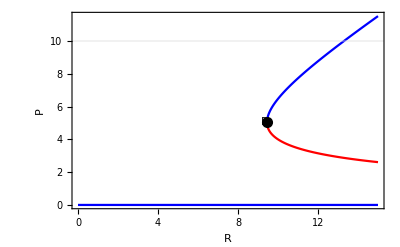

```mathematica
Show[DisplayBifurcationDiagram[PR,R,MaxStepSize->0.1],GridLines->{{},{10.0}}]
```

```mathematica
$BifurcationDiagramBPs
```

{BifurcationPoint[Fold,{5.03968419957949},{R→9.44940787421155}]}

### Slopes of the Chemical Gradients

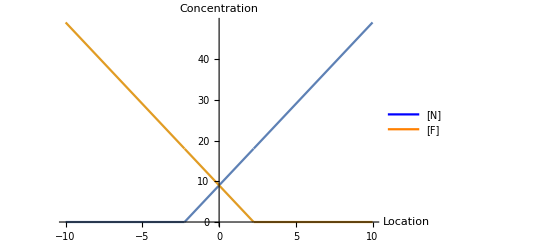

```mathematica
Plot[{If[(4x)+9<0,0,(4x)+9],If[-4x+9<0,0,-4x+9]},{x,-10.0,10.0},AxesLabel->{"Location","Concentration"},PlotLegends->LineLegend[{Blue,Orange},{"[N]","[F]"}]]
```

### Trajectories for the Chemotaxing Protocell

```mathematica
OrigPC1 = OrigPC/.{kd->0.05,γ->0.04,K1->4,h->20,α->1,n->3,K2->0.5,V->2,C1->9,S->4};
```

```mathematica
Show[DisplayTrajectories[OrigPC1,{{5,6,0.5,1}},200,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Orange}],
DisplayTrajectories[OrigPC1,{{15,3,0.5,0}},100,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Purple,Dashed,Thick}],
DisplayTrajectories[OrigPC1,{{7.349758134564639,5.721987371393649,0.23903332092221824,3.8102825061052408}},200,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Blue,Thick}],
LabelStyle->Directive[Black, 12],AxesLabel->{Style["[A]","Text"],Style["[B]","Text"],Style["L","Text"]}]
```

-Graphics3D-

## Analyses for IEEE SSCI (December 7th, 2022)

In this section I show how I made the various animations of the protocell trajectories for my presentation. I also partially illustrate a few things that I did not have space for in the paper or the presentation, such as the protocell having terminal trajectories that shoot through the limit cycle, and there being a saddle cycle that divides the phase space.

### Phase Portraits with Viability Region Shading for the Protocell (No Behavior)

```mathematica
PC1 = PC/.{kd->0.05,γ->0.04,K1->4,h->3,F->10};
```

```mathematica
Manipulate[DisplayPhasePortrait[PC1/.{N1->conc,F->conc},NullManifolds->True, Tries->60 ],{{conc,0},0,25}]
```

```mathematica
Animation=Table[DisplayPhasePortrait[PC1/.{N1->conc,F->conc},NullManifolds->True, Tries->60 ],{conc,0,25,0.25}];
```

```mathematica
Export["protobif.gif",Animation]
```

```mathematica
ExpandFileName["protobif.gif"]
```

```mathematica
PC2 = PC/.{kd->0.05,γ->0.04,K1->4,h->3,N1->5,F->5};
PC3 = PC/.{kd->0.05,γ->0.04,K1->4,h->3,N1->12,F->12};
PC4 = PC/.{kd->0.05,γ->0.04,K1->4,h->3,N1->30,F->6};
PC5 = PC/.{kd->0.05,γ->0.04,K1->4,h->3,N1->14,F->14};
```

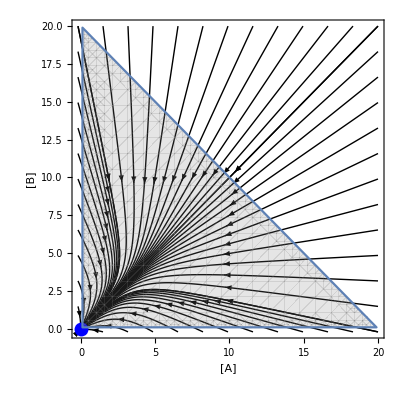

```mathematica
Quiet[Show[DisplayFlow[PC2,100,PlotStyle->Black,FlowPlotMode->Boundary],DisplayPhasePortrait[PC2],
RegionPlot[A+B<=20&&A>=0.1&&B>=0.1,{A,0,20},{B,0,20},PlotStyle->Directive[Opacity[0.2],Gray]],LabelStyle->Directive[Black, 12],FrameLabel->{"[A]","[B]"}]]
```

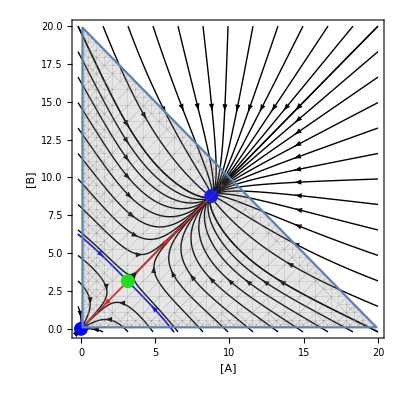

```mathematica
Quiet[Show[DisplayFlow[PC3,100,PlotStyle->Black,FlowPlotMode->Boundary],DisplayPhasePortrait[PC3,SaddleManifolds->True,SaddleManifoldDuration->600,SaddleManifoldPlotPoints->100,Tries->100],RegionPlot[A+B<=20&&A>=0.1&&B>=0.1,{A,0,20},{B,0,20},PlotStyle->Directive[Opacity[0.2],Gray]],LabelStyle->Directive[Black, 12],FrameLabel->{"[A]","[B]"}]]
```

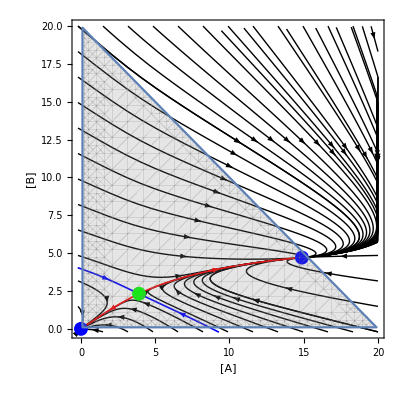

```mathematica
Quiet[Show[DisplayFlow[PC4,100,PlotStyle->Black,FlowPlotMode->Boundary],DisplayPhasePortrait[PC4,SaddleManifolds->True,SaddleManifoldDuration->600,SaddleManifoldPlotPoints->100,Tries->100],RegionPlot[A+B<=20&&A>=0.1&&B>=0.1,{A,0,20},{B,0,20},PlotStyle->Directive[Opacity[0.2],Gray]],LabelStyle->Directive[Black, 12],FrameLabel->{"[A]","[B]"}]]
```

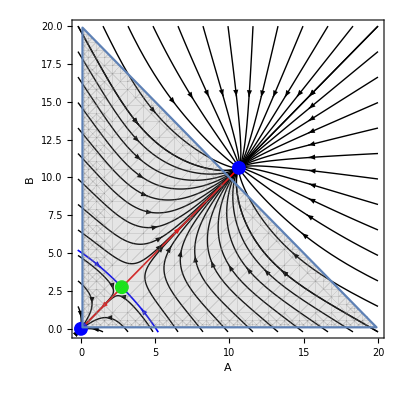

```mathematica
Quiet[Show[DisplayFlow[PC5,100,PlotStyle->Black,FlowPlotMode->Boundary],DisplayPhasePortrait[PC5,SaddleManifolds->True,SaddleManifoldDuration->600,SaddleManifoldPlotPoints->100,Tries->100],RegionPlot[A+B<=20&&A>=0.1&&B>=0.1,{A,0,20},{B,0,20},PlotStyle->Directive[Opacity[0.2],Gray]]]]
```

### Animating a Chemotaxing Protocell

```mathematica
Show[DisplayTrajectories[OrigPC1,{{5,6,0.5,1}},200,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Orange}],
DisplayTrajectories[OrigPC1,{{15,3,0.5,0}},100,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Purple,Dashed,Thick}],
DisplayTrajectories[OrigPC1,{{7.349758134564639,5.721987371393649,0.23903332092221824,3.8102825061052408}},200,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Blue,Thick}],
DisplayTrajectories[OrigPC1,{{10.3,10,0.5,0}},150,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Red,Thick}],
LabelStyle->Directive[Black, 12],AxesLabel->{Style["[A]","Text"],Style["[B]","Text"],Style["L","Text"]}]
```

-Graphics3D-

```mathematica
Show[DisplayTrajectories[OrigPC1,{{5,6,0.5,1}},200,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Orange}],
DisplayTrajectories[OrigPC1,{{15,3,0.5,0}},100,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Purple,Dashed,Thick}],
DisplayTrajectories[OrigPC1,{{7.349758134564639,5.721987371393649,0.23903332092221824,3.8102825061052408}},200,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Blue,Thick}],
DisplayTrajectories[OrigPC1,{{16,16,0.5,0}},800,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Green,Thick}],
LabelStyle->Directive[Black, 12],AxesLabel->{Style["[A]","Text"],Style["[B]","Text"],Style["L","Text"]}]
```

-Graphics3D-

#### Animating Survival Behavior

```mathematica
DisplayTrajectories[OrigPC1,{{7.349758134564639,5.721987371393649,0.23903332092221824,3.8102825061052408}},25,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Blue,Thick}]
```

-Graphics3D-

```mathematica
Animation=Table[Show[DisplayTrajectories[OrigPC1,{{7.349758134564639,5.721987371393649,0.23903332092221824,3.8102825061052408}},25,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Blue,Thick}],
DisplayTrajectories[OrigPC1,{{1,10,0.5,0}},time,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Gray}],
DisplayTrajectories[OrigPC1,{{10,1,0.5,0}},time,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Gray}],
DisplayTrajectories[OrigPC1,{{5,7,0.5,0}},time,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Gray}],
DisplayTrajectories[OrigPC1,{{7,5,0.5,0}},time,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Gray}],
LabelStyle->Directive[Black, 12],AxesLabel->{Style["[A]","Text"],Style["[B]","Text"],Style["L","Text"]}
],{time,0,600,12}];
```

```mathematica
Export["survival.gif",Animation]
```

survival.gif

```mathematica
ExpandFileName["survival.gif"]
```

C:\Users\conno\Documents\survival.gif

### Animation of Decay

```mathematica
Animation=Table[Show[DisplayTrajectories[OrigPC1,{{7.349758134564639,5.721987371393649,0.23903332092221824,3.8102825061052408}},25,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Blue,Thick}],
DisplayTrajectories[OrigPC1,{{5,6,0.5,0}},time,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Orange}],
DisplayTrajectories[OrigPC1,{{6,5,0.5,0}},time,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Orange}],
LabelStyle->Directive[Black, 12],AxesLabel->{Style["[A]","Text"],Style["[B]","Text"],Style["L","Text"]},PlotRange->{{0,10},{0,10},{-10,10}}
],{time,0,200,4}];
```

```mathematica
Export["decay.gif",Animation]
```

decay.gif

```mathematica
ExpandFileName["decay.gif"]
```

C:\Users\conno\Documents\decay.gif

### Animation of Bursting

```mathematica
Animation=Table[Show[DisplayTrajectories[OrigPC1,{{7.349758134564639,5.721987371393649,0.23903332092221824,3.8102825061052408}},25,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Blue,Thick}],
DisplayTrajectories[OrigPC1,{{15,3,0.5,0}},time,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Black}],
DisplayTrajectories[OrigPC1,{{3,15,0.5,0}},time,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B,L},PlotStyle->{Black}],
LabelStyle->Directive[Black, 12],AxesLabel->{Style["[A]","Text"],Style["[B]","Text"],Style["L","Text"]},PlotRange->{{0,16},{0,16},{-10,10}}
],{time,0,300,6}];
```

```mathematica
Export["burst.gif",Animation]
```

burst.gif

```mathematica
ExpandFileName["burst.gif"]
```

C:\Users\conno\Documents\burst.gif

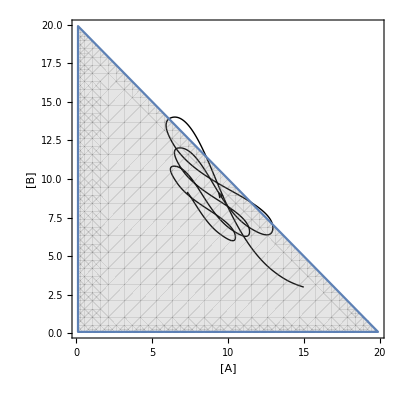

```mathematica
Show[DisplayTrajectories[OrigPC1,{{15,3,0.5,0}},100,MaxSteps->15000,PlotPoints->20000,PlotRange->All,BoxRatios->{1,1},StateVariables->{A,B},PlotStyle->{Black,Thick}],
RegionPlot[A+B<=20&&A>=0.1&&B>=0.1,{A,0,20},{B,0,20},PlotStyle->Directive[Opacity[0.2],Gray]],
LabelStyle->Directive[Black, 12],FrameLabel->{"[A]","[B]"}]
```